# Метод обратной параболической интерполяции

Выполнил:Cайков Константин 
 Группа:ПМ1801

```mathematica
parabolINTER[xn2_,xn1_,xn_,f]:=(f[xn1]*f[xn]*xn2)/((f[xn2]-f[xn1])*(f[xn2]-f[xn]))+ (f[xn2]*f[xn]*xn1)/((f[xn1]-f[xn2])*(f[xn1]-f[xn]))+(f[xn2]*f[xn1]*xn)/((f[xn]-f[xn2])*(f[xn]-f[xn1]))
```

```mathematica
f[x_]:=x^3+6 x^2+6x+1
```

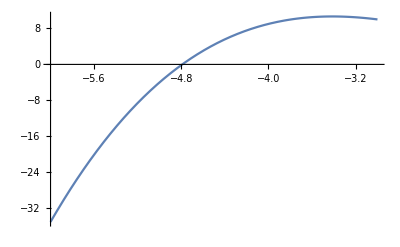

```mathematica
Plot[f[x],{x,-6,-3}]
```

```mathematica
xn2 = -21;
xn1 = -11;
xn  = -8;
prom = parabolINTER[xn2,xn1,xn,f]
prov = False;
While[Abs[f[prom]-0]≥  1, 
Print[N@prom];
xn2= xn1;
xn1 = xn;
xn = prom;
prom = parabolINTER[xn2,xn1,xn,f];
]
Print["Ответ:", N@prom ]
```

-13879843/2023131

-6.86058

-5.74202

-5.13403

-4.86537

Ответ:-4.79649

```mathematica
N@Solve[x^3+6 x^2+6x+1== 0,x]
```

{{x→-1.},{x→-4.79129},{x→-0.208712}}